```mathematica
Mi={{1, x0, x0^2, x0^3}, {1, x1, x1^2, x1^3}, {1, x2, x2^2, x2^3}, {1, x3, x3^2, x3^3}}
```

{{1,x0,x0^2,x0^3},{1,x1,x1^2,x1^3},{1,x2,x2^2,x2^3},{1,x3,x3^2,x3^3}}

```mathematica
Me={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
Mi[[;;,4]]=Mi[[;;,4]]-Mi[[;;,3]]x0;
(*Me[[;;,4]]=Me[[;;,4]]-Me[[;;,3]]x0;*)
Mi[[;;,3]]=Mi[[;;,3]]-Mi[[;;,2]]x0;
(*Me[[;;,3]]=Me[[;;,3]]-Me[[;;,2]]x0;*)
Mi[[;;,2]]=Mi[[;;,2]]-Mi[[;;,1]]x0;
(*Me[[;;,2]]=Me[[;;,2]]-Me[[;;,1]]x0;*)
Mi[[2,;;]]=Mi[[2,;;]]-Mi[[1,;;]];
Me[[2,;;]]=Me[[2,;;]]-Me[[1,;;]];
Mi[[3,;;]]=Mi[[3,;;]]-Mi[[1,;;]];
Me[[3,;;]]=Me[[3,;;]]-Me[[1,;;]];
Mi[[4,;;]]=Mi[[4,;;]]-Mi[[1,;;]];
Me[[4,;;]]=Me[[4,;;]]-Me[[1,;;]];
Mi[[2,;;]]=Mi[[2,;;]]/(x1-x0);
Me[[2,;;]]=Me[[2,;;]]/(x1-x0);
Mi[[3,;;]]=Mi[[3,;;]]/(x2-x0);
Me[[3,;;]]=Me[[3,;;]]/(x2-x0);
Mi[[4,;;]]=Mi[[4,;;]]/(x3-x0);
Me[[4,;;]]=Me[[4,;;]]/(x3-x0);
Mi=Mi//Simplify;
Me=Me//Simplify;
Mi[[;;,4]]=Mi[[;;,4]]-Mi[[;;,3]]x1;
(*Me[[;;,4]]=Me[[;;,4]]-Me[[;;,3]]x1;*)
Mi[[;;,3]]=Mi[[;;,3]]-Mi[[;;,2]]x1;
(*Me[[;;,3]]=Me[[;;,3]]-Me[[;;,2]]x1;*)
Mi[[3,;;]]=Mi[[3,;;]]-Mi[[2,;;]];
Me[[3,;;]]=Me[[3,;;]]-Me[[2,;;]];
Mi[[4,;;]]=Mi[[4,;;]]-Mi[[2,;;]];
Me[[4,;;]]=Me[[4,;;]]-Me[[2,;;]];
Mi[[3,;;]]=Mi[[3,;;]]/(x2-x1);
Me[[3,;;]]=Me[[3,;;]]/(x2-x1);
Mi[[4,;;]]=Mi[[4,;;]]/(x3-x1);
Me[[4,;;]]=Me[[4,;;]]/(x3-x1);
Mi=Mi//Simplify;
Me=Me//Simplify;
Mi[[;;,4]]=Mi[[;;,4]]-Mi[[;;,3]]x2;
(*Me[[;;,4]]=Me[[;;,4]]-Me[[;;,3]]x2;*)
Mi[[4,;;]]=Mi[[4,;;]]-Mi[[3,;;]];
Me[[4,;;]]=Me[[4,;;]]-Me[[3,;;]];
Mi[[4,;;]]=Mi[[4,;;]]/(x3-x2);
Me[[4,;;]]=Me[[4,;;]]/(x3-x2);
Mi=Mi//Simplify;
Me[[3,;;]]-=(Me[[4,;;]]x2);
Me[[2,;;]]-=(Me[[3,;;]]x1);
Me[[3,;;]]-=(Me[[4,;;]]x1);
Me[[1,;;]]-=(Me[[2,;;]]x0);
Me[[2,;;]]-=(Me[[3,;;]]x0);
Me[[3,;;]]-=(Me[[4,;;]]x0);
Me=Me//Simplify;
```

```mathematica
Mi//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Me//MatrixForm
```

(-(x1 x2 x3)/((x0-x1) (x0-x2) (x0-x3)) | (x0 x2 x3)/((x0-x1) (x1-x2) (x1-x3)) | (x0 x1 x3)/((x0-x2) (-x1+x2) (x2-x3)) | (x0 x1 x2)/((x0-x3) (-x1+x3) (-x2+x3))
(x2 x3+x1 (x2+x3))/((x0-x1) (x0-x2) (x0-x3)) | -(x2 x3+x0 (x2+x3))/((x0-x1) (x1-x2) (x1-x3)) | -(x1 x3+x0 (x1+x3))/((x0-x2) (-x1+x2) (x2-x3)) | -(x1 x2+x0 (x1+x2))/((x0-x3) (-x1+x3) (-x2+x3))
-(x1+x2+x3)/((x0-x1) (x0-x2) (x0-x3)) | (x0+x2+x3)/((x0-x1) (x1-x2) (x1-x3)) | (x0+x1+x3)/((x0-x2) (-x1+x2) (x2-x3)) | (x0+x1+x2)/((x0-x3) (-x1+x3) (-x2+x3))
1/((x0-x1) (x0-x2) (x0-x3)) | -1/((x0-x1) (x1-x2) (x1-x3)) | -1/((x0-x2) (-x1+x2) (x2-x3)) | 1/((-x0+x3) (-x1+x3) (-x2+x3)))

```mathematica
Me[[2,4]]//Expand
```

-(x0 x1)/(x0-x1)-(x0 x2)/(x0-x1)-(x1 x2)/(x0-x1)-(x0 x1 x2)/(x0-x1)

```mathematica
Me[[3,2]]//Expand
```

1/((x0-x1) (-x1+x2))+x0/((x0-x1) (-x1+x2))+x0/((-x0+x2) (-x1+x2))

```mathematica
Me[[3,3]]//Expand
```

x0/((x0-x1) (x0-x2) (x1-x2))+x0^2/((x0-x1) (x0-x2) (x1-x2))-x1/((x0-x1) (x0-x2) (x1-x2))+(x0 x1)/((x0-x1) (x0-x2) (x1-x2))+(x0 x1^2)/((x0-x1) (x0-x2) (x1-x2))-(x0 x2)/((x0-x1) (x0-x2) (x1-x2))-(x1 x2)/((x0-x1) (x0-x2) (x1-x2))-(x0 x1 x2)/((x0-x1) (x0-x2) (x1-x2))

```mathematica
Mi={{1, x0, x0^2}, {1, x1, x1^2}, {1, x2, x2^2}}
```

{{1,x0,x0^2},{1,x1,x1^2},{1,x2,x2^2}}

```mathematica
Inverse[{{1, x0, x0^2}, {1, x1, x1^2}, {1, x2, x2^2}}]//Simplify//MatrixForm
```

((x1 x2)/((x0-x1) (x0-x2)) | -(x0 x2)/((x0-x1) (x1-x2)) | (x0 x1)/((x0-x2) (x1-x2))
-(x1+x2)/((x0-x1) (x0-x2)) | (x0+x2)/((x0-x1) (x1-x2)) | (x0+x1)/((x0-x2) (-x1+x2))
1/((x0-x1) (x0-x2)) | -1/((x0-x1) (x1-x2)) | 1/((x0-x2) (x1-x2)))

```mathematica
Inverse[{{1, x0, x0^2, x0^3}, {1, x1, x1^2, x1^3}, {1, x2, x2^2, x2^3}, {1, x3, x3^2, x3^3}}]//Simplify//MatrixForm
```

(-(x1 x2 x3)/((x0-x1) (x0-x2) (x0-x3)) | (x0 x2 x3)/((x0-x1) (x1-x2) (x1-x3)) | (x0 x1 x3)/((x0-x2) (-x1+x2) (x2-x3)) | (x0 x1 x2)/((x0-x3) (-x1+x3) (-x2+x3))
(x2 x3+x1 (x2+x3))/((x0-x1) (x0-x2) (x0-x3)) | -(x2 x3+x0 (x2+x3))/((x0-x1) (x1-x2) (x1-x3)) | -(x1 x3+x0 (x1+x3))/((x0-x2) (-x1+x2) (x2-x3)) | -(x1 x2+x0 (x1+x2))/((x0-x3) (-x1+x3) (-x2+x3))
-(x1+x2+x3)/((x0-x1) (x0-x2) (x0-x3)) | (x0+x2+x3)/((x0-x1) (x1-x2) (x1-x3)) | (x0+x1+x3)/((x0-x2) (-x1+x2) (x2-x3)) | (x0+x1+x2)/((x0-x3) (-x1+x3) (-x2+x3))
1/((x0-x1) (x0-x2) (x0-x3)) | -1/((x0-x1) (x1-x2) (x1-x3)) | 1/((x0-x2) (x1-x2) (x2-x3)) | -1/((x0-x3) (-x1+x3) (-x2+x3)))

```mathematica
Inverse[{{1, x1}, {1, x2}}]//MatrixForm
```

(x2/(-x1+x2) | -x1/(-x1+x2)
-1/(-x1+x2) | 1/(-x1+x2))

```mathematica
Me={{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Mi[[;;,3]]=Mi[[;;,3]]-Mi[[;;,2]]x0;
Me[[;;,3]]=Me[[;;,3]]-Me[[;;,2]]x0;
Mi[[;;,2]]=Mi[[;;,2]]-Mi[[;;,1]]x0;
Me[[;;,2]]=Me[[;;,2]]-Me[[;;,1]]x0;
Mi[[2,;;]]=Mi[[2,;;]]-Mi[[1,;;]];
Me[[2,;;]]=Me[[2,;;]]-Me[[1,;;]];
Mi[[3,;;]]=Mi[[3,;;]]-Mi[[1,;;]];
Me[[3,;;]]=Me[[3,;;]]-Me[[1,;;]];
Mi[[2,;;]]=Mi[[2,;;]]/(x1-x0);
Me[[2,;;]]=Me[[2,;;]]/(x1-x0);
Mi[[3,;;]]=Mi[[3,;;]]/(x2-x0);
Me[[3,;;]]=Me[[3,;;]]/(x2-x0);
Mi=Mi//Simplify;
Me=Me//Simplify;
Mi[[;;,3]]=Mi[[;;,3]]-Mi[[;;,2]]x1;
Me[[;;,3]]=Me[[;;,3]]-Me[[;;,2]]x1;
Mi[[3,;;]]=Mi[[3,;;]]-Mi[[2,;;]];
Me[[3,;;]]=Me[[3,;;]]-Me[[2,;;]];
Mi[[3,;;]]=Mi[[3,;;]]/(x2-x1);
Me[[3,;;]]=Me[[3,;;]]/(x2-x1);
Mi=Mi//Simplify;
Me=Me//Simplify;
```

```mathematica
Mi//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Me//MatrixForm
```

(1 | -x0 | x0 x1
1/(x0-x1) | (1+x0)/(-x0+x1) | (x0+x1+x0 x1)/(x0-x1)
1/((x0-x1) (x0-x2)) | ((1+x0)/(x0-x1)+x0/(-x0+x2))/(-x1+x2) | (x0^2-x1 (1+x2)+x0 (1+x1+x1^2-x2-x1 x2))/((x0-x1) (x0-x2) (x1-x2)))

```mathematica
MMe=Inverse[{{1, x0, x0^2}, {1, x1, x1^2}, {1, x2, x2^2}}]//Simplify
```

{{(x1 x2)/((x0-x1) (x0-x2)),-(x0 x2)/((x0-x1) (x1-x2)),(x0 x1)/((x0-x2) (x1-x2))},{-(x1+x2)/((x0-x1) (x0-x2)),(x0+x2)/((x0-x1) (x1-x2)),(x0+x1)/((x0-x2) (-x1+x2))},{1/((x0-x1) (x0-x2)),-1/((x0-x1) (x1-x2)),1/((x0-x2) (x1-x2))}}

```mathematica
MMe//MatrixForm
```

((x1 x2)/((x0-x1) (x0-x2)) | -(x0 x2)/((x0-x1) (x1-x2)) | (x0 x1)/((x0-x2) (x1-x2))
-(x1+x2)/((x0-x1) (x0-x2)) | (x0+x2)/((x0-x1) (x1-x2)) | (x0+x1)/((x0-x2) (-x1+x2))
1/((x0-x1) (x0-x2)) | -1/((x0-x1) (x1-x2)) | 1/((x0-x2) (x1-x2)))

```mathematica
MMe.{{1, x0, x0^2}, {1, x1, x1^2}, {1, x2, x2^2}}//Simplify
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
MMe=Me/.{x0->1,x1->2,x2->3}
```

{{1,-1,2},{-1,2,-5},{1/2,-3/2,9/2}}

```mathematica
{{1, x0, x0^2}, {1, x1, x1^2}, {1, x2, x2^2}}/.{x0->1,x1->2,x2->3}
```

{{1,1,1},{1,2,4},{1,3,9}}

```mathematica
a={1,2,1}.MMe
```

{-1/2,3/2,-7/2}

```mathematica
a.{1,x,x^2}/.x->2
```

-23/2

```mathematica
M={{1, x0, x0^2}, {1, x1, x1^2}, {1, x2, x2^2}}
```

{{1,x0,x0^2},{1,x1,x1^2},{1,x2,x2^2}}

```mathematica
Mi=Inverse[M]//Simplify
```

{{(x1 x2)/((x0-x1) (x0-x2)),-(x0 x2)/((x0-x1) (x1-x2)),(x0 x1)/((x0-x2) (x1-x2))},{-(x1+x2)/((x0-x1) (x0-x2)),(x0+x2)/((x0-x1) (x1-x2)),(x0+x1)/((x0-x2) (-x1+x2))},{1/((x0-x1) (x0-x2)),-1/((x0-x1) (x1-x2)),1/((x0-x2) (x1-x2))}}

```mathematica
Mi.M//Simplify
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Mc=M/.{x0->1,x1->2,x2->3}
```

{{1,1,1},{1,2,4},{1,3,9}}

```mathematica
Mic=Mi/.{x0->1,x1->2,x2->3}
```

{{3,-3,1},{-5/2,4,-3/2},{1/2,-1,1/2}}

```mathematica
Mic//MatrixForm
```

(3 | -3 | 1
-5/2 | 4 | -3/2
1/2 | -1 | 1/2)

```mathematica
Mc//MatrixForm
```

(1 | 1 | 1
1 | 2 | 4
1 | 3 | 9)

```mathematica
a=Mic.{1,2,1}
```

{-2,4,-1}

```mathematica
Mc.a
```

{1,2,1}

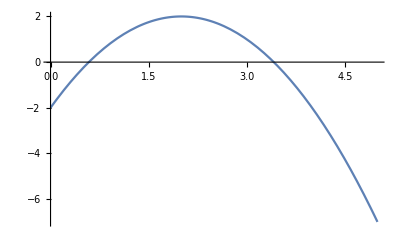

```mathematica
Plot[-x^2+4x-2,{x,-0,5}]
```